# Box diagrams

## Load FeynCalc

```mathematica
description="Learning FeynCalc through examples.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

Successfully patched FeynArts.

```mathematica
$KeepLogDivergentScalelessIntegrals = True;
```

```mathematica
$ToolsRoot=ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$ToolsRoot,"Include"}]];
<<Tools`
<<PrettyNotation`
```

```mathematica
MakeBoxes[p1,TraditionalForm]:=SubscriptBox["p","1"];
MakeBoxes[p2,TraditionalForm]:=SubscriptBox["p","2"];
MakeBoxes[k1,TraditionalForm]:=SubscriptBox["k","1"];
MakeBoxes[k2,TraditionalForm]:=SubscriptBox["k","2"];
MakeBoxes[m1,TraditionalForm]:=SubscriptBox["m","1"];
MakeBoxes[m2,TraditionalForm]:=SubscriptBox["m","2"];
MakeBoxes[m3,TraditionalForm]:=SubscriptBox["m","3"];
MakeBoxes[μZ,TraditionalForm]:=SubscriptBox["μ","Z"];
MakeBoxes[ΓZ,TraditionalForm]:=SubscriptBox["Γ","Z"];
MakeBoxes[x0,TraditionalForm]:=SubscriptBox["x","0"];
MakeBoxes[x1,TraditionalForm]:=SubscriptBox["x","1"];
MakeBoxes[x2,TraditionalForm]:=SubscriptBox["x","2"];
MakeBoxes[xγ,TraditionalForm]:=SubscriptBox["x","γ"];
MakeBoxes[u1,TraditionalForm]:=SubscriptBox["u","1"];
MakeBoxes[u2,TraditionalForm]:=SubscriptBox["u","2"];
MakeBoxes[uγ,TraditionalForm]:=SubscriptBox["u","γ"];
MakeBoxes[z1,TraditionalForm]:=SubscriptBox["z","1"];
MakeBoxes[z2,TraditionalForm]:=SubscriptBox["z","2"];
MakeBoxes[zγ,TraditionalForm]:=SubscriptBox["z","γ"];
MakeBoxes[a1,TraditionalForm]:=SubscriptBox["a","1"];
MakeBoxes[a2,TraditionalForm]:=SubscriptBox["a","2"];
MakeBoxes[aγ,TraditionalForm]:=SubscriptBox["a","γ"];
MakeBoxes[β1,TraditionalForm]:=SubscriptBox["β","1"];
MakeBoxes[β2,TraditionalForm]:=SubscriptBox["β","2"];
MakeBoxes[xp,TraditionalForm]:=SuperscriptBox["x","+"];
MakeBoxes[xm,TraditionalForm]:=SuperscriptBox["x","-"];
MakeBoxes[λs,TraditionalForm]:=SubscriptBox["λ","s"];
MakeBoxes[λQ,TraditionalForm]:=SubscriptBox["λ","Q"];
MakeBoxes[c1,TraditionalForm]:=SubscriptBox["c","1"];
MakeBoxes[c2,TraditionalForm]:=SubscriptBox["c","2"];
```

## Draw diagrams

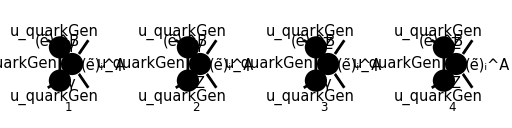

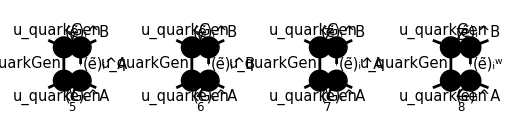

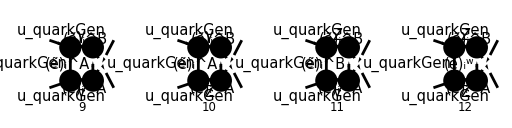

```mathematica
diagsBox[0]=InsertFields[
CreateTopologies[1,2->2,BoxesOnly],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],
V[3],
F[11|12],
S[11|13|14]
}
];
Paint[
diagsBox[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

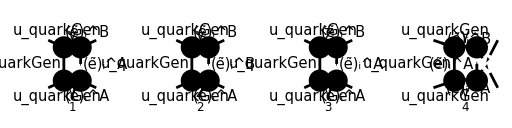

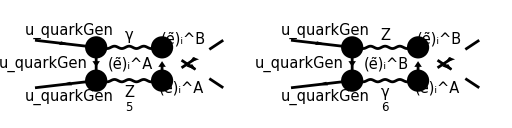

```mathematica
diagsBox[1]=DiagramExtract[diagsBox[0],{5,6,7,9,10,11}];
Paint[
diagsBox[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

## Preliminaries

```mathematica
myAssumptions={
m1∈PositiveReals,
m2∈PositiveReals,
SMP["m_Z"]∈PositiveReals,
ΓZ∈PositiveReals,
s∈PositiveReals,
δ∈PositiveReals,
λ∈PositiveReals,
m1^2-t>0,
m2^2-t>0,
m1^2-u>0,
m2^2-u>0
};
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,m1,m2];
safeTrickMandelstam[expr_]:=TrickMandelstam[expr,{s,t,u,m1^2+m2^2+δ}]
fullTrickMandelstam[expr_]:=TrickMandelstam[expr,{s,t,u,m1^2+m2^2}]
```

```mathematica
mZtoBW[expr_]:=ReplaceAll[expr,SMP["m_Z"]->Sqrt[SMP["m_Z"]^2-I SMP["m_Z"] ΓZ]]
mZtoμZ[expr_]:=ReplaceAll[expr,SMP["m_Z"]->μZ]
```

## Amplitudes

```mathematica
MboxList[0]=FCFAConvert[
CreateFeynAmp[diagsBox[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->False,
List->True,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->D
]/.{MQU[quarkGen]->0,MSf[B,2,i]->m1,MSf[A,2,i]->m2}//ZSimplify//mZtoμZ
```

{-((ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ρ e δ_Col1Col2).(γ·k).(-2/3 ⅈ γ^μ e).(φ(p_1)) IndexDelta(A,B) g^μν (-k-k_1+k_2-p_2)^ν g^ρσ (k-2 k_2+p_2)^σ e^2)/(16 π^4 k^2.(k+p_2)^2.((k-k_2+p_2)^2-m_2^2).(k-k_1-k_2+p_2)^2)),-((ⅈ Z_l_i^AB (φ(-p_2)).(2 ⅈ (Z_q_R γ^ρ.(γ̄)^6+Z_q_L γ^ρ.(γ̄)^7) e δ_Col1Col2)/((cos(θ_W)) (sin(θ_W))).(γ·k).(-2/3 ⅈ γ^μ e).(φ(p_1)) g^μν (-k-k_1+k_2-p_2)^ν g^ρσ (k-2 k_2+p_2)^σ e^2)/(16 π^4 k^2.((k+p_2)^2-μ_Z^2).((k-k_2+p_2)^2-m_1^2).(k-k_1-k_2+p_2)^2 (cos(θ_W)) (sin(θ_W)))),-((ⅈ Z_l_i^AB (φ(-p_2)).(-2/3 ⅈ γ^ρ e δ_Col1Col2).(γ·k).(2 ⅈ (Z_q_R γ^μ.(γ̄)^6+Z_q_L γ^μ.(γ̄)^7) e)/((cos(θ_W)) (sin(θ_W))).(φ(p_1)) g^μν (-k-k_1+k_2-p_2)^ν g^ρσ (k-2 k_2+p_2)^σ e^2)/(16 π^4 k^2.(k+p_2)^2.((k-k_2+p_2)^2-m_2^2).((k-k_1-k_2+p_2)^2-μ_Z^2) (cos(θ_W)) (sin(θ_W)))),-((ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ρ e δ_Col1Col2).(γ·k).(-2/3 ⅈ γ^μ e).(φ(p_1)) IndexDelta(A,B) g^μν (-k+k_1-k_2-p_2)^ν g^ρσ (k-2 k_1+p_2)^σ e^2)/(16 π^4 k^2.(k+p_2)^2.((k-k_1+p_2)^2-m_2^2).(k-k_1-k_2+p_2)^2)),-((ⅈ Z_l_i^AB (φ(-p_2)).(2 ⅈ (Z_q_R γ^ρ.(γ̄)^6+Z_q_L γ^ρ.(γ̄)^7) e δ_Col1Col2)/((cos(θ_W)) (sin(θ_W))).(γ·k).(-2/3 ⅈ γ^μ e).(φ(p_1)) g^μν (-k+k_1-k_2-p_2)^ν g^ρσ (k-2 k_1+p_2)^σ e^2)/(16 π^4 k^2.((k+p_2)^2-μ_Z^2).((k-k_1+p_2)^2-m_2^2).(k-k_1-k_2+p_2)^2 (cos(θ_W)) (sin(θ_W)))),-((ⅈ Z_l_i^AB (φ(-p_2)).(-2/3 ⅈ γ^ρ e δ_Col1Col2).(γ·k).(2 ⅈ (Z_q_R γ^μ.(γ̄)^6+Z_q_L γ^μ.(γ̄)^7) e)/((cos(θ_W)) (sin(θ_W))).(φ(p_1)) g^μν (-k+k_1-k_2-p_2)^ν g^ρσ (k-2 k_1+p_2)^σ e^2)/(16 π^4 k^2.(k+p_2)^2.((k-k_1+p_2)^2-m_1^2).((k-k_1-k_2+p_2)^2-μ_Z^2) (cos(θ_W)) (sin(θ_W))))}

### Photon--photon amplitude

```mathematica
Mγ[0]=(MboxList[0][[{1,4}]]//Total)(3/2SMP["e_Q"])^2//Contract//FullSimplify//FeynAmpDenominatorSplit//FCE//ReplaceAll[#,{
FAD[{k-k1+p2,m2}]->FAD[{k-k1+p2,m1}],
FAD[k-k1-k2+p2]->FAD[k-p1]
}]&//FeynAmpDenominatorCombine//DiracGammaExpand//FCE//ReplaceAll[#,GSD[k2]->GSD[p1+p2-k1]]&//DiracGammaCombine
Mγ[1]=Mγ[0]//DiracSimplify//FullSimplify[#,Assumptions->myAssumptions]&//TID[#,k,ToPaVe->True]&//Collect2[#,{A0,B0,C0,D0},Factoring->Simplify,IsolateNames->KK]&
```

(ⅈ e^4 e_Q^2 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k-2 k_1+p_2)).(γ·k).(γ·(-k+2 k_1-p_1-2 p_2)).(φ(p_1)))/(16 π^4 k^2.(k-p_1)^2.(k+p_2)^2.((k-k_1+p_2)^2-m_1^2))+(ⅈ e^4 e_Q^2 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k+2 k_1-2 p_1-p_2)).(γ·k).(γ·(-k-2 k_1+p_1)).(φ(p_1)))/(16 π^4 k^2.(k-p_1)^2.(k+p_2)^2.((k-k_2+p_2)^2-m_2^2))

1/16 KK(6601) B_0(-m_1^2+s+t+u,0,m_1^2)+1/16 KK(6638) B_0(-m_2^2+s+t+u,0,m_2^2)-1/16 KK(6569) B_0(m_1^2,0,m_1^2)-1/16 KK(6604) B_0(m_2^2,0,m_2^2)+1/16 KK(6635) B_0(s,0,0)+1/16 KK(6562) C_0(m_1^2,s,-m_1^2+s+t+u,m_1^2,0,0)+1/8 KK(6566) C_0(0,u,-m_1^2+s+t+u,0,0,m_1^2)+1/16 KK(6579) C_0(m_2^2,s,-m_2^2+s+t+u,m_2^2,0,0)-1/8 KK(6595) C_0(0,t,-m_2^2+s+t+u,0,0,m_2^2)+1/8 KK(6633) C_0(0,m_2^2,t,0,0,m_2^2)-1/8 KK(6598) C_0(0,m_1^2,u,0,0,m_1^2)+1/8 KK(6622) C_0(0,0,s,0,0,0)+1/8 KK(6587) D_0(0,0,m_2^2,-m_2^2+s+t+u,s,t,0,0,0,m_2^2)-1/8 KK(6627) D_0(0,0,m_1^2,-m_1^2+s+t+u,s,u,0,0,0,m_1^2)

```mathematica
MγUV[0]=Mγ[1]//PaXEvaluateUV[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FRH//FullSimplify
MγIR[0]=Mγ[1]//ReplaceAll[#,{m1->m,m2->m}]&//Collect2[#,{A0,B0,C0,D0},IsolateNames->KK]&//TrickMandelstam[#,{s,t,u,2m^2}]&//PaXEvaluateIR[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,{EpsilonIR},Factoring->Function[expr,Simplify[PowerExpand[TrickMandelstam[ReplaceAll[expr,{m1->m,m2->m}],{s,t,u,2m^2}]]]],IsolateNames->KK]&//FRH//ReplaceAll[#,Log[a_]-Log[b_]->Log[a/b]]&//ReplaceAll[#,Log[(m^2-t)/(m^2-u)]->1/2Log[(m1^2-t)(m2^2-t)/((m1^2-u)(m2^2-u))]]&
```

0

(e^4 e_Q^2 δ_Col1Col2 IndexDelta(A,B) log(((m_1^2-t) (m_2^2-t))/((m_1^2-u) (m_2^2-u))) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(4 π^2 s ε_IR)

Notice in the last replacement we use that m1=m2, and that Log[x]=1/2 (Log[x]+Log[x])

```mathematica
MγIR[1]=MγIR[0]/(2SMP["e"]^2SMP["e_Q"]IndexDelta[A,B]SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]]SpinorVBarD[p2].GSD[k1].SpinorUD[p1]/s)MγLO//DiracSimplify
```

(e^2 MγLO e_Q log(((m_1^2-t) (m_2^2-t))/((m_1^2-u) (m_2^2-u))))/(8 π^2 ε_IR)

### Photon--Z-boson amplitude

```mathematica
MZ[0]=(MboxList[0][[{2,3,5,6}]]//Total)3/2SMP["e_Q"]//Contract//FullSimplify//FeynAmpDenominatorSplit//FCE//ReplaceAll[#,{
FAD[{k-k1-k2+p2,μZ}]->FAD[{k-p1,μZ}],
FAD[k-k1-k2+p2]->FAD[k-p1],
FAD[{k-k1+p2,m2}]->FAD[{k+k2-p1,m2}],
FAD[{k-k2+p2,m1}]->FAD[{k+k1-p1,m1}]
}]&//FeynAmpDenominatorCombine//DiracGammaExpand//FCE//ReplaceAll[#,GSD[k2]->GSD[p1+p2-k1]]&//DiracGammaCombine
MZ[1]=MZ[0]//DiracSimplify//FullSimplify[#,Assumptions->myAssumptions]&//TID[#,k,ToPaVe->True]&//Collect2[#,{A0,B0,C0,D0},Factoring->Simplify,IsolateNames->KK]&
```

-((ⅈ e^4 e_Q δ_Col1Col2 Z_l_i^AB (φ(-p_2)).(Z_q_L (γ·(k+2 k_1-2 p_1-p_2)).(γ̄)^7+Z_q_R (γ·(k+2 k_1-2 p_1-p_2)).(γ̄)^6).(γ·k).(γ·(-k-2 k_1+p_1)).(φ(p_1)))/(8 π^4 (cos(θ_W))^2 (sin(θ_W))^2 k^2.(k-p_1)^2.((k+p_2)^2-μ_Z^2).((k+k_1-p_1)^2-m_1^2)))-(ⅈ e^4 e_Q δ_Col1Col2 Z_l_i^AB (φ(-p_2)).(Z_q_L (γ·(k-2 k_1+p_2)).(γ̄)^7+Z_q_R (γ·(k-2 k_1+p_2)).(γ̄)^6).(γ·k).(γ·(-k+2 k_1-p_1-2 p_2)).(φ(p_1)))/(8 π^4 (cos(θ_W))^2 (sin(θ_W))^2 k^2.(k-p_1)^2.((k+p_2)^2-μ_Z^2).((k+k_2-p_1)^2-m_2^2))-(ⅈ e^4 e_Q δ_Col1Col2 Z_l_i^AB (φ(-p_2)).(γ·(k-2 k_1+p_2)).(γ·k).(Z_q_L (γ·(-k+2 k_1-p_1-2 p_2)).(γ̄)^7+Z_q_R (γ·(-k+2 k_1-p_1-2 p_2)).(γ̄)^6).(φ(p_1)))/(8 π^4 (cos(θ_W))^2 (sin(θ_W))^2 k^2.((k-p_1)^2-μ_Z^2).(k+p_2)^2.((k-k_1+p_2)^2-m_1^2))-(ⅈ e^4 e_Q δ_Col1Col2 Z_l_i^AB (φ(-p_2)).(γ·(k+2 k_1-2 p_1-p_2)).(γ·k).(Z_q_L (γ·(-k-2 k_1+p_1)).(γ̄)^7+Z_q_R (γ·(-k-2 k_1+p_1)).(γ̄)^6).(φ(p_1)))/(8 π^4 (cos(θ_W))^2 (sin(θ_W))^2 k^2.((k-p_1)^2-μ_Z^2).(k+p_2)^2.((k-k_2+p_2)^2-m_2^2))

-1/8 KK(33599) C_0(m_2^2,s,-m_2^2+s+t+u,m_2^2,0,μ_Z^2)+1/8 KK(33602) C_0(m_1^2,s,-m_1^2+s+t+u,m_1^2,0,μ_Z^2)-1/4 KK(33648) C_0(0,u,-m_2^2+s+t+u,μ_Z^2,0,m_2^2)+1/4 KK(33653) C_0(0,t,-m_2^2+s+t+u,μ_Z^2,0,m_2^2)+1/4 KK(33660) C_0(0,t,-m_1^2+s+t+u,μ_Z^2,0,m_1^2)-1/4 KK(33666) C_0(0,u,-m_1^2+s+t+u,μ_Z^2,0,m_1^2)-1/4 KK(33656) C_0(0,m_2^2,t,0,0,m_2^2)-1/4 KK(33658) C_0(0,m_1^2,t,0,0,m_1^2)+1/4 KK(33670) C_0(0,m_1^2,u,0,0,m_1^2)-1/4 KK(33676) C_0(0,m_2^2,u,0,0,m_2^2)+1/4 KK(33604) C_0(0,0,s,0,0,μ_Z^2)-1/4 KK(33608) D_0(0,0,m_1^2,-m_1^2+s+t+u,s,t,μ_Z^2,0,0,m_1^2)+1/4 KK(33626) D_0(0,0,m_2^2,-m_2^2+s+t+u,s,t,μ_Z^2,0,0,m_2^2)-1/4 KK(33643) D_0(0,0,m_2^2,-m_2^2+s+t+u,s,u,μ_Z^2,0,0,m_2^2)+1/4 KK(33663) D_0(0,0,m_1^2,-m_1^2+s+t+u,s,u,μ_Z^2,0,0,m_1^2)

```mathematica
MZUV[0]=MZ[1]//PaXEvaluateUV[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
MZIR[0]=MZ[1]//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//PaXEvaluateIR[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,EpsilonIR,
Factoring->Function[expr,
FullSimplify[TrickMandelstam[DiracSimplify[expr],{s,t,u,m1^2+m2^2}],Assumptions->myAssumptions]
],IsolateNames->KK]&//FRH//ReplaceAll[#,Log[a_]->-Log[1/a]]&
```

0

-(e^4 e_Q δ_Col1Col2 Z_l_i^AB log(((m_1^2-t) (t-m_2^2))/((m_1^2-u) (u-m_2^2))) (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))))/(2 π^2 ε_IR (cos(θ_W))^2 (s-μ_Z^2) (sin(θ_W))^2)

The last replacement is done to get the same logarithm expression as the two-photon case.

```mathematica
MZIR[1]=MZIR[0]/(-2SMP["e"]^2ZliAB/(SMP["sin_W"]^2SMP["cos_W"]^2(s-μZ^2))SpinorVBarD[p2].GSD[k1].(Zql(1-GAD[5])+Zqr(1+GAD[5])).SpinorUD[p1])MZLO//DiracSimplify//FullSimplify
```

(e^2 MZLO e_Q δ_Col1Col2 log(((m_1^2-t) (t-m_2^2))/((m_1^2-u) (u-m_2^2))))/(8 π^2 ε_IR)

### IR divergence summarized

```mathematica
MγIR[1]
MZIR[1]
```

(e^2 MγLO e_Q log(((m_1^2-t) (m_2^2-t))/((m_1^2-u) (m_2^2-u))))/(8 π^2 ε_IR)

(e^2 MZLO e_Q δ_Col1Col2 log(((m_1^2-t) (t-m_2^2))/((m_1^2-u) (u-m_2^2))))/(8 π^2 ε_IR)

### Wait... It’s all zero!

```mathematica
Mγ[1]//ReplaceAll[#,{m1->m,m2->m}]&//Collect2[#,{A0,B0,C0,D0},IsolateNames->KK]&//TrickMandelstam[#,{s,t,u,2m^2}]&//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D),PaXC0Expand->True]&//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->Function[expr,Simplify[PowerExpand[TrickMandelstam[ReplaceAll[expr,{m1->m,m2->m}],{s,t,u,2m^2}]]]],IsolateNames->KK]&//FRH//FCE//ReplaceAll[#,GSD[k2]->GSD[p1+p2-k1]]&//DiracSimplify//Simplify//TrickMandelstam[#,{s,t,u,2m^2}]&//Collect2[#,{t,u},IsolateNames->KK]&;
%+(%//ReplaceAll[#,{t->u,u->t}]&)//FRH//FullSimplify
```

0

```mathematica
MZ[1]//FRH//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//ReplaceAll[#,k2->p1+p2-k1]&//DiracSimplify//Collect2[#,{t,u,m1,m2},IsolateNames->KK]&;
%+(%//ReplaceAll[#,{t->u,u->t,m1->m2,m2->m1}]&)//Simplify
```

0

## Triangles

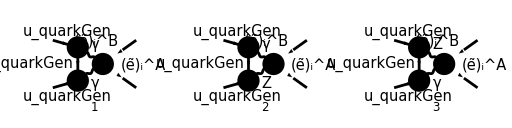

```mathematica
diagsTriangle[0]=DiagramExtract[diagsBox[0],{1,2,3}];
Paint[
diagsTriangle[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
MTriangleList[0]=FCFAConvert[
CreateFeynAmp[diagsTriangle[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->False,
List->True,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->D
]/.{MQU[quarkGen]->0,MSf[B,2,i]->m1,MSf[A,2,i]->m2}//ZSimplify//mZtoμZ
```

{-(ⅈ e^2 g^μν g^νσ g^ρσ IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^ρ δ_Col1Col2).(γ·k).(-2/3 ⅈ e γ^μ).(φ(p_1)))/(8 π^4 k^2.(k+p_2)^2.(k-k_1-k_2+p_2)^2),-(ⅈ e^2 g^μν g^νσ g^ρσ Z_l_i^AB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (γ^ρ.(γ̄)^7 Z_q_L+γ^ρ.(γ̄)^6 Z_q_R))/((cos(θ_W)) (sin(θ_W))).(γ·k).(-2/3 ⅈ e γ^μ).(φ(p_1)))/(8 π^4 (cos(θ_W)) (sin(θ_W)) k^2.((k+p_2)^2-μ_Z^2).(k-k_1-k_2+p_2)^2),-(ⅈ e^2 g^μν g^νσ g^ρσ Z_l_i^AB (φ(-p_2)).(-2/3 ⅈ e γ^ρ δ_Col1Col2).(γ·k).(2 ⅈ e (γ^μ.(γ̄)^7 Z_q_L+γ^μ.(γ̄)^6 Z_q_R))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(8 π^4 (cos(θ_W)) (sin(θ_W)) k^2.(k+p_2)^2.((k-k_1-k_2+p_2)^2-μ_Z^2))}

```mathematica
MTriangle[0]=(MTriangleList[0]//Total)(3/2SMP["e_Q"])^2//Contract//DiracSimplify//FullSimplify
MTriangle[1]=MTriγ[0]//TID[#,k,ToPaVe->True]&//FullSimplify//fullTrickMandelstam
MTriangle[2]=MTriangle[1]//DiracGammaExpand//FCE//ReplaceAll[#,GSD[k2]->GSD[p1+p2-k1]]&//DiracSimplify
```

1/(8 π^4 (cos(θ_W))^2 (sin(θ_W))^2)ⅈ (D-2) e^4 e_Q^2 δ_Col1Col2 (3 Z_l_i^AB (1/(k^2.(k+p_2)^2.((k-k_1-k_2+p_2)^2-μ_Z^2))+1/(k^2.((k+p_2)^2-μ_Z^2).(k-k_1-k_2+p_2)^2)) (Z_q_L (φ(-p_2)).(γ·k).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k).(γ̄)^6.(φ(p_1)))-((cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2)).(γ·k).(φ(p_1)))/(k^2.(k+p_2)^2.(k-k_1-k_2+p_2)^2))

-1/(8 π^2 s)(2-D) e^4 e_Q^2 δ_Col1Col2 IndexDelta(A,B) (-B_0(0,0,0) (φ(-p_2)).(-(γ·(k_1+k_2-p_2))).(φ(p_1))+B_0(s,0,0) (φ(-p_2)).(-(γ·(k_1+k_2-2 p_2))).(φ(p_1))-B_0(0,0,0) (φ(-p_2)).(γ·p_2).(φ(p_1)))

0